```mathematica
$RecursionLimit=Infinity

collatz[1]=1

collatz[n_Integer/;And[n>1,OddQ[n]]]:=collatz[n]=3 n+1
collatz[n_Integer/;And[n>1,EvenQ[n]]]:=collatz[n]=n/2

collatzseq[1]={1}
collatzseq[n_Integer/;n>1]:=collatzseq[n]={n,Splice@collatzseq@collatz@n}

collatzseq[9780657630];
```

∞

1

{1}

```mathematica
map[n_Integer/;OddQ[n]]:=o
map[n_Integer/;EvenQ[n]]:=e
```

```mathematica
Grid@
Tally@
Map[map,collatzseq[9780657630]]
```

e | 707
o | 426

```mathematica
n/2
```

n/2

```mathematica
NestList[#/2&,n,10]
```

{n,n/2,n/4,n/8,n/16,n/32,n/64,n/128,n/256,n/512,n/1024}

```mathematica
With[{c1=0.25,c2=0.618},ineqs={{c1+w[1]+x[1]≤x[2],c1+w[1]+x[1]≤x[3],c1+w[1]+x[1]≤x[4],c1+w[1]+x[1]≤x[5],c1+w[1]+x[1]≤x[6],c1+w[1]+x[1]≤x[7],c1+w[2]+x[2]≤x[3],c1+w[4]+x[4]≤x[5],c1+w[2]+x[2]≤x[3],c1+w[2]+x[2]≤x[5],c1+w[2]+x[2]≤x[7],c1+w[4]+x[4]≤x[3],c1+w[4]+x[4]≤x[5],c1+w[4]+x[4]≤x[7],c1+w[6]+x[6]≤x[5],c1+w[8]+x[8]≤x[4],c1+w[9]+x[9]≤x[4],c1+w[10]+x[10]≤x[4],c1+w[10]+x[10]≤x[6],c1+w[6]+x[6]≤x[7],c1+w[8]+x[8]≤x[9],c1+w[8]+x[8]≤x[10],x[1]≥0,x[8]≥0,w[3]+x[3]≤𝓌,w[5]+x[5]≤𝓌,w[7]+x[7]≤𝓌},{c1+h[1]+y[1]≤y[6],c1+h[1]+y[1]≤y[7],c1+h[1]+y[1]≤y[8],c1+h[1]+y[1]≤y[9],c1+h[1]+y[1]≤y[10],c1+h[2]+y[2]≤y[4],c1+h[2]+y[2]≤y[9],c1+h[4]+y[4]≤y[6],c1+h[3]+y[3]≤y[5],c1+h[5]+y[5]≤y[7],c1+h[9]+y[9]≤y[6],c1+h[9]+y[9]≤y[10],y[1]≥0,y[2]≥0,y[3]≥0,h[6]+y[6]≤𝒽,h[7]+y[7]≤𝒽,h[8]+y[8]≤𝒽,h[10]+y[10]≤𝒽},{c2≤h[1]/w[1]≤(1+c2),c2≤h[2]/w[2]≤(1+c2),c2≤h[3]/w[3]≤(1+c2),c2≤h[4]/w[4]≤(1+c2),c2≤h[5]/w[5]≤(1+c2),c2≤h[6]/w[6]≤(1+c2),c2≤h[7]/w[7]≤(1+c2),c2≤h[8]/w[8]≤(1+c2),c2≤h[9]/w[9]≤(1+c2),c2≤h[10]/w[10]≤(1+c2)},{h[1] w[1]==1,h[2] w[2]==2,h[3] w[3]==3,h[4] w[4]==4,h[5] w[5]==5,h[6] w[6]==6,h[7] w[7]==7,h[8] w[8]==8,h[9] w[9]==9,h[10] w[10]==10}}];
```

```mathematica
%13
```

{{0.25+w[1]+x[1]≤x[2],0.25+w[1]+x[1]≤x[3],0.25+w[1]+x[1]≤x[4],0.25+w[1]+x[1]≤x[5],0.25+w[1]+x[1]≤x[6],0.25+w[1]+x[1]≤x[7],0.25+w[2]+x[2]≤x[3],0.25+w[4]+x[4]≤x[5],0.25+w[2]+x[2]≤x[3],0.25+w[2]+x[2]≤x[5],0.25+w[2]+x[2]≤x[7],0.25+w[4]+x[4]≤x[3],0.25+w[4]+x[4]≤x[5],0.25+w[4]+x[4]≤x[7],0.25+w[6]+x[6]≤x[5],0.25+w[8]+x[8]≤x[4],0.25+w[9]+x[9]≤x[4],0.25+w[10]+x[10]≤x[4],0.25+w[10]+x[10]≤x[6],0.25+w[6]+x[6]≤x[7],0.25+w[8]+x[8]≤x[9],0.25+w[8]+x[8]≤x[10],x[1]≥0,x[8]≥0,w[3]+x[3]≤𝓌,w[5]+x[5]≤𝓌,w[7]+x[7]≤𝓌},{0.25+h[1]+y[1]≤y[6],0.25+h[1]+y[1]≤y[7],0.25+h[1]+y[1]≤y[8],0.25+h[1]+y[1]≤y[9],0.25+h[1]+y[1]≤y[10],0.25+h[2]+y[2]≤y[4],0.25+h[2]+y[2]≤y[9],0.25+h[4]+y[4]≤y[6],0.25+h[3]+y[3]≤y[5],0.25+h[5]+y[5]≤y[7],0.25+h[9]+y[9]≤y[6],0.25+h[9]+y[9]≤y[10],y[1]≥0,y[2]≥0,y[3]≥0,h[6]+y[6]≤𝒽,h[7]+y[7]≤𝒽,h[8]+y[8]≤𝒽,h[10]+y[10]≤𝒽},{0.618≤h[1]/w[1]≤1.618,0.618≤h[2]/w[2]≤1.618,0.618≤h[3]/w[3]≤1.618,0.618≤h[4]/w[4]≤1.618,0.618≤h[5]/w[5]≤1.618,0.618≤h[6]/w[6]≤1.618,0.618≤h[7]/w[7]≤1.618,0.618≤h[8]/w[8]≤1.618,0.618≤h[9]/w[9]≤1.618,0.618≤h[10]/w[10]≤1.618},{h[1] w[1]==1,h[2] w[2]==2,h[3] w[3]==3,h[4] w[4]==4,h[5] w[5]==5,h[6] w[6]==6,h[7] w[7]==7,h[8] w[8]==8,h[9] w[9]==9,h[10] w[10]==10}}

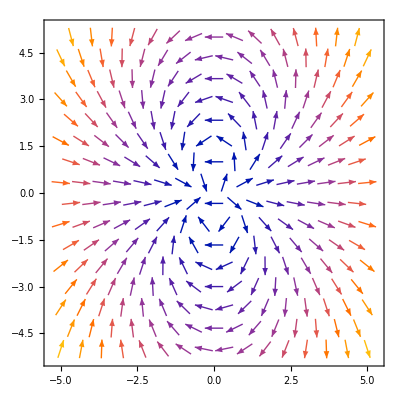

```mathematica
VectorPlot[{2 x^2-y^2,3 x y},{x,-5,5},{y,-5,5}]
```

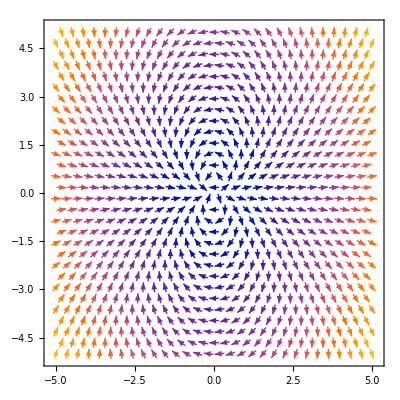

```mathematica
VectorPlot[{2 x^2-y^2,3 x y},{x,-5,5},{y,-5,5},VectorPoints->30]
```

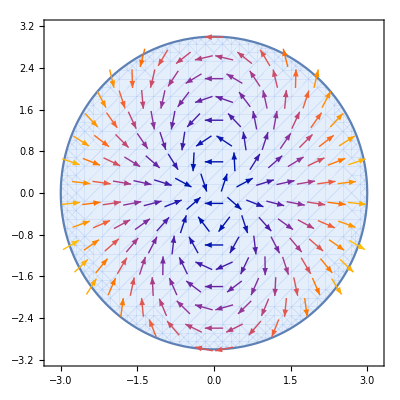

```mathematica
VectorPlot[{2 x^2-y^2,3 x y},{x,y}∈Disk[{0,0},3]]
```

```mathematica
MeshConnectivityGraph[Dodecahedron[],0]
```

-Graphics3D-

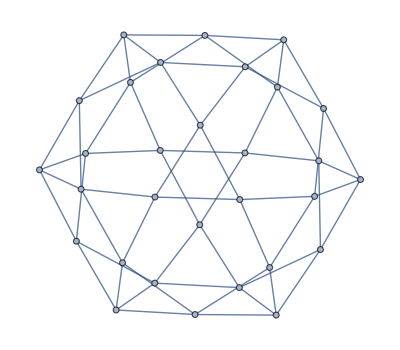

```mathematica
MeshConnectivityGraph[Dodecahedron[],1]
```

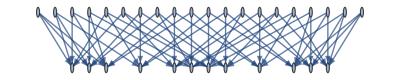

```mathematica
MeshConnectivityGraph[Dodecahedron[],{0,2}]
```

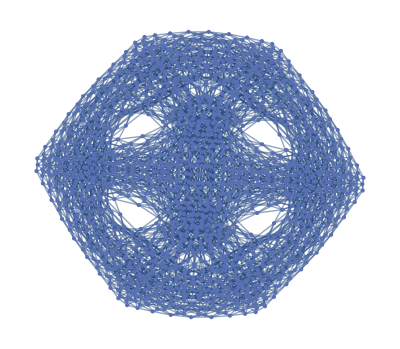
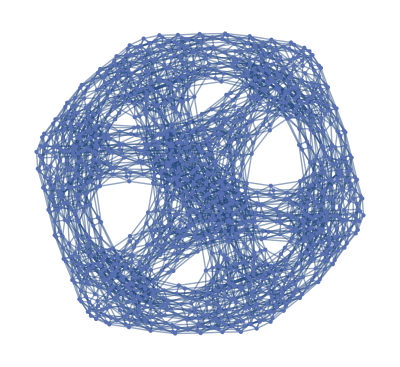
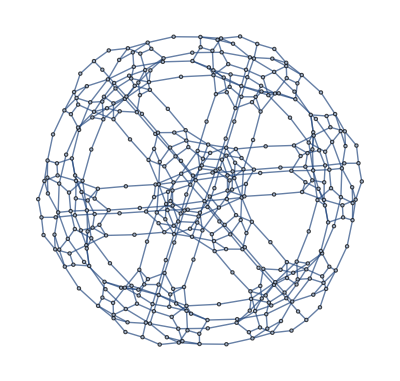
{-Graphics3D-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[MeshConnectivityGraph[MengerMesh[2,3],d],{d,0,3}]
```

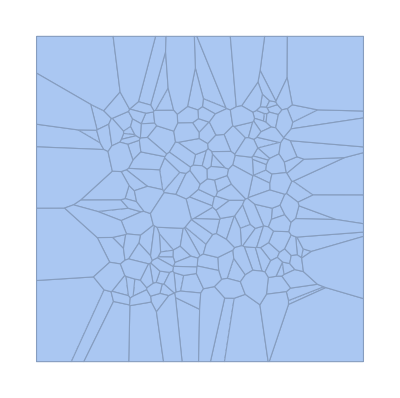

```mathematica
vm=VoronoiMesh[RandomReal[1,{200,2}]]
```

```mathematica
Graph[{Annotation[x,"age"->10],Annotation[y,"age"->20]},{x->y,y->x,y->y}]
```

-Graphics-

```mathematica
{a,b,Nothing,c,Nothing}
```

{a,b,c}

```mathematica
SubsetCases[{a,b,a,b,a,c},{x_,y_,x_},Overlaps->True]
```

{{a,b,a},{a,b,a},{a,a,a},{a,c,a},{a,b,a},{a,b,a},{a,c,a},{b,a,b},{b,a,b},{b,a,b},{b,c,b},{a,b,a},{a,b,a},{a,c,a}}